1/(1+ⅇ^(1/(-1+x)+1/x))

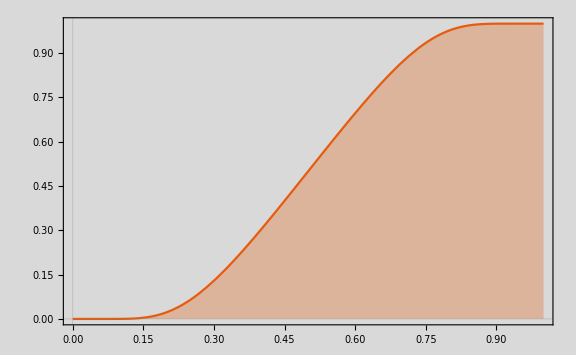

```mathematica
g[x_]=Exp[(-1/x)];
h[x_]=g[x]/(g[x]+g[1-x]) //FullSimplify
Plot[h[x],{x,0,1},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

Piecewise[{{0, x≤0}, {1/(1+ⅇ^(1/(-1+x)+1/x)), 0<x<1}, {1, 1≤x}, {0, True}}]

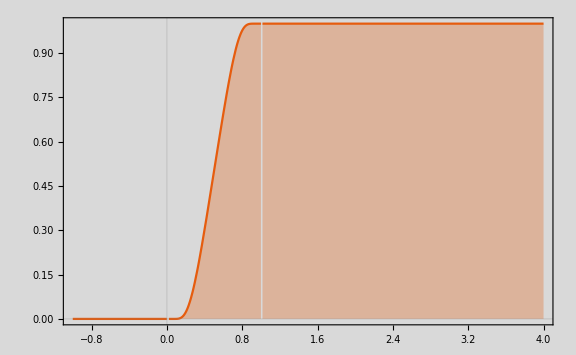

```mathematica
d[x_]=Piecewise[{{0,x<=0},{h[x],0<x<1},{1,1<=x}}]
Plot[d[x],{x,-1,4},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

```mathematica
d'[x]//FullSimplify
```

Piecewise[{{(2+4 (-1+x) x)/(4 (-1+x)^2 x^2 (1+Cosh[1/(-1+x)+1/x])), 0<x<1}, {0, True}}]